# Google PageRankの計算 (概要)

リンク構造に着目し、各ページの”点数”を計算し、これにもとづきランクを決定する

初期の重みなしリンクのネットワーク状態を、重みつきリンクのネットワーク状態に計算し直すことで”点数”が得られ、点数が高いほど重要なページとみなされる

計算には繰り返し法が用いられる

素朴に計算を行うと0点のページがたくさんできるが、”ランダムサーファーモデル”を導入して回避している

## Nav: top | prev | next

## ネットワーク状態変化のアニメーション:

以上webコンテンツ

## プログラム

```mathematica
toAdjacency[t_]:=Map[If[#>0,1,0]&,t,{2}]
```

```mathematica
ellipseLayout[n_,{a_,b_}]:=Table[{a Cos[2Pi/n u],b Sin[2Pi/n u]},{u,1,n}]
```

```mathematica
MtoH[m_]:=Map[If[Tr[#]==0,#,#/Tr[#]]&,m]
```

```mathematica
MtoS[m_]:=Module[{l},
l=Dimensions[m][[2]];
Map[If[Tr[#]==0,Table[1/l,{l}],#/Tr[#]]&,m]
]
```

```mathematica
StoG[m_,a_]:=m*a+(1-a)/Length[m]
```

```mathematica
MtoG[m_,a_]:=MtoS[m]*a+(1-a)/Length[m]
```

```mathematica
nextScore[score_,m_]:=Map[Tr[#]&,Transpose[m*score]]
```

```mathematica
zeroSelf[mat_]:=ReplacePart[mat,Table[{n,n}->0,{n,Length[mat]}]]
```

## 定義と例示

nextScore[]の繰り返し適応によるscoreの収束によって返されるベクトルの各要素が言わば、各ページのスコアです。このスコアが高いほど影響力が高いとされます。MtoH[]とStoG[]のaに注目してみましょう。この操作により、もとが疎行列であってもスコアの低いページのスコアが0に落ち込むことを防ぎます。これはランダムサーファーモデルと言われています。

早速、例を見てみます。ノード数を8として、ランダムに隣接行列を作成します。自身へのリンクは0に置き換えています。

```mathematica
l={{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0}}
```

{{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0}}

```mathematica
vnames["l"]=Table[IntegerString[n,"Roman"],{n,Length[l]}]
```

{I,II,III,IV,V,VI,VII,VIII}

```mathematica
vlabels["l"]=Table[n->Text[Style[IntegerString[n,"Roman"],Large]],{n,Length[l]}]
```

{1→I,2→II,3→III,4→IV,5→V,6→VI,7→VII,8→VIII}

```mathematica
(*(l=ReplacePart[Table[RandomChoice[{1,0,0,0,0}],{8},{8}],Table[{n,n}->0,{n,8}]])//TableForm*)
```

以下は隣接行列からのグラフ表示です。

### スライド0

```mathematica
tb["m"]=TableForm[l,TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,3.4}]
```

| I | II | III | IV | V | VI | VII | VIII
I | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
II | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
III | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
IV | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
V | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
VII | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
VIII | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0

```mathematica
gr["m"]=AdjacencyGraph[l,VertexCoordinates->ellipseLayout[8,{1.4,1}],VertexLabels->vlabels["l"],ImagePadding->{{10,60},{10,20}},ImageSize->{320,320}]
```

-Graphics-

```mathematica
score["m"]=Map[Tr[#]&,Transpose[l]]
```

{1,3,2,1,1,0,0,0}

```mathematica
ranking["m"]=Ordering[Ordering[score["m"],All,Greater]]
```

{5,1,2,4,3,8,7,6}

```mathematica
rt["m"]=TableForm[Inner[List,score["m"],ranking["m"],List],TableHeadings->{vnames["l"],{"点数","rank"}}]
```

| 点数 | rank
I | 1 | 5
II | 3 | 1
III | 2 | 2
IV | 1 | 4
V | 1 | 3
VI | 0 | 8
VII | 0 | 7
VIII | 0 | 6

```mathematica
txt["m"]=Graphics[{FontSize->16,Text[Style["左上: 基となるネットワーク、
リンク数は少ない。

左下: その結合行列、
列(たて)方向の数値を
足すと\"点数\"となる。

下: ランク表
",TextAlignment->Left]]},ImageSize->{240,260}];
```

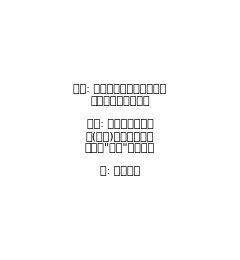
-Graphics- | -Graphics-
 | I | II | III | IV | V | VI | VII | VIII
I | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
II | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
III | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
IV | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
V | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
VII | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
VIII | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 |  | 点数 | rank
I | 1 | 5
II | 3 | 1
III | 2 | 2
IV | 1 | 4
V | 1 | 3
VI | 0 | 8
VII | 0 | 7
VIII | 0 | 6

```mathematica
slide[0]=Grid[{{gr["m"],txt["m"]},{tb["m"],rt["m"]}},Alignment->{{Center,Center},{Top,Bottom}}]
```

### スライド1

```mathematica
g[0]=MtoG[l,0.9]
```

{{0.0125,0.0125,0.9125,0.0125,0.0125,0.0125,0.0125,0.0125},{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125},{0.0125,0.9125,0.0125,0.0125,0.0125,0.0125,0.0125,0.0125},{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125},{0.0125,0.9125,0.0125,0.0125,0.0125,0.0125,0.0125,0.0125},{0.0125,0.0125,0.0125,0.0125,0.9125,0.0125,0.0125,0.0125},{0.9125,0.0125,0.0125,0.0125,0.0125,0.0125,0.0125,0.0125},{0.0125,0.3125,0.3125,0.3125,0.0125,0.0125,0.0125,0.0125}}

```mathematica
tb["g",0]=TableForm[Round[g[0],0.001],TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,1}]
```

| I | II | III | IV | V | VI | VII | VIII
I | 0.012 | 0.012 | 0.912 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012
II | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
III | 0.012 | 0.912 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012
IV | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
V | 0.012 | 0.912 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012
VI | 0.012 | 0.012 | 0.012 | 0.012 | 0.912 | 0.012 | 0.012 | 0.012
VII | 0.912 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012
VIII | 0.012 | 0.312 | 0.312 | 0.312 | 0.012 | 0.012 | 0.012 | 0.012

```mathematica
edgeforce["g",0]=MapIndexed[If[#>0,{#2,#1}]&,g[0],{2}];
```

```mathematica
style["g",0]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/50])&,Cases[edgeforce["g",0],_List,{2}]];
```

```mathematica
gr["g",0]=AdjacencyGraph[toAdjacency[g[0]],VertexCoordinates->ellipseLayout[8,{1.4,1}],VertexLabels->vlabels["l"],DirectedEdges->True,EdgeStyle->style["g",0],ImagePadding->{{5,5},{5,5}},ImageSize->{320,320}]
```

-Graphics-

```mathematica
score["g",0]=Map[Tr[#]&,Transpose[g[0]]]
```

{1.225,2.425,1.525,0.625,1.225,0.325,0.325,0.325}

```mathematica
ranking["g",0]=Ordering[Ordering[score["g",0],All,Greater]]
```

{4,1,2,5,3,8,7,6}

```mathematica
rt["g",0]=TableForm[Inner[List,score["g",0],ranking["g",0],List],TableHeadings->{vnames["l"],{"点数","rank"}}]
```

| 点数 | rank
I | 1.225 | 4
II | 2.425 | 1
III | 1.525 | 2
IV | 0.625 | 5
V | 1.225 | 3
VI | 0.325 | 8
VII | 0.325 | 7
VIII | 0.325 | 6

```mathematica
txt["g",0]=Graphics[{FontSize->16,Text[Style["左上: ランダムサーファー
モデルにより密結合された
ネットワーク(リンクの強さ
を線の太さで表してある)、
すべてのノードがリンク
されている。

左下: その結合行列

下: ランク表",TextAlignment->Left]]},ImageSize->{240,280}];
```

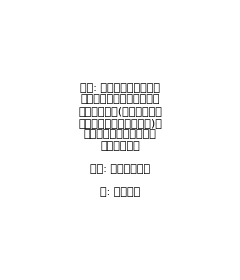
-Graphics- | -Graphics-
 | I | II | III | IV | V | VI | VII | VIII
I | 0.012 | 0.012 | 0.912 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012
II | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
III | 0.012 | 0.912 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012
IV | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
V | 0.012 | 0.912 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012
VI | 0.012 | 0.012 | 0.012 | 0.012 | 0.912 | 0.012 | 0.012 | 0.012
VII | 0.912 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012 | 0.012
VIII | 0.012 | 0.312 | 0.312 | 0.312 | 0.012 | 0.012 | 0.012 | 0.012 |  | 点数 | rank
I | 1.225 | 4
II | 2.425 | 1
III | 1.525 | 2
IV | 0.625 | 5
V | 1.225 | 3
VI | 0.325 | 8
VII | 0.325 | 7
VIII | 0.325 | 6

```mathematica
slide[1]=Grid[{{gr["g",0],txt["g",0]},{tb["g",0],rt["g",0]}},Alignment->{{Center,Center},{Top,Top}}]
```

### スライド2

```mathematica
PGscore["g",1]=Nest[nextScore[#,MtoG[l,0.9]]&,Table[1/8,{8}],1]
```

{0.153125,0.303125,0.190625,0.078125,0.153125,0.040625,0.040625,0.040625}

```mathematica
(g[1]=MtoG[l,0.9]*PGscore["g",1])//TableForm
```

0.00191406 | 0.00191406 | 0.139727 | 0.00191406 | 0.00191406 | 0.00191406 | 0.00191406 | 0.00191406
0.0378906 | 0.0378906 | 0.0378906 | 0.0378906 | 0.0378906 | 0.0378906 | 0.0378906 | 0.0378906
0.00238281 | 0.173945 | 0.00238281 | 0.00238281 | 0.00238281 | 0.00238281 | 0.00238281 | 0.00238281
0.00976563 | 0.00976563 | 0.00976563 | 0.00976563 | 0.00976563 | 0.00976563 | 0.00976563 | 0.00976563
0.00191406 | 0.139727 | 0.00191406 | 0.00191406 | 0.00191406 | 0.00191406 | 0.00191406 | 0.00191406
0.000507812 | 0.000507812 | 0.000507812 | 0.000507812 | 0.0370703 | 0.000507812 | 0.000507812 | 0.000507812
0.0370703 | 0.000507812 | 0.000507812 | 0.000507812 | 0.000507812 | 0.000507812 | 0.000507812 | 0.000507812
0.000507812 | 0.0126953 | 0.0126953 | 0.0126953 | 0.000507812 | 0.000507812 | 0.000507812 | 0.000507812

```mathematica
tb["g",1]=TableForm[Round[g[1],0.001],TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,1}]
```

| I | II | III | IV | V | VI | VII | VIII
I | 0.002 | 0.002 | 0.14 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002
II | 0.038 | 0.038 | 0.038 | 0.038 | 0.038 | 0.038 | 0.038 | 0.038
III | 0.002 | 0.174 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002
IV | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01
V | 0.002 | 0.14 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002
VI | 0.001 | 0.001 | 0.001 | 0.001 | 0.037 | 0.001 | 0.001 | 0.001
VII | 0.037 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
VIII | 0.001 | 0.013 | 0.013 | 0.013 | 0.001 | 0.001 | 0.001 | 0.001

```mathematica
edgeforce["g",1]=MapIndexed[If[#>0,{#2,#1}]&,g[1],{2}];
```

```mathematica
style["g",1]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/10])&,Cases[edgeforce["g",1],_List,{2}]];
```

```mathematica
gr["g",1]=AdjacencyGraph[toAdjacency[g[1]],VertexCoordinates->ellipseLayout[8,{1.4,1}],VertexLabels->vlabels["l"],DirectedEdges->True,EdgeStyle->style["g",1],ImagePadding->{{5,5},{5,5}},ImageSize->{320,320}]
```

-Graphics-

```mathematica
score["g",1]=Map[Tr[#]&,Transpose[g[1]]]
```

{0.0919531,0.376953,0.205391,0.0675781,0.0919531,0.0553906,0.0553906,0.0553906}

```mathematica
ranking["g",1]=Ordering[Ordering[score["g",1],All,Greater]]
```

{4,1,2,5,3,8,7,6}

```mathematica
rt["g",1]=TableForm[Inner[List,Round[score["g",1],0.001],ranking["g",1],List],TableHeadings->{vnames["l"],{"点数","rank"}}]
```

| 点数 | rank
I | 0.092 | 4
II | 0.377 | 1
III | 0.205 | 2
IV | 0.068 | 5
V | 0.092 | 3
VI | 0.055 | 8
VII | 0.055 | 7
VIII | 0.055 | 6

```mathematica
txt["g",1]=Graphics[{FontSize->16,Text[Style["左上: ランダムサーファー
モデルにより密結合された
ネットワークに、1回繰り
返し法を適応したもの、
リンクの強さが変化してい
ることがわかる。

左下: その結合行列

下: ランク表",TextAlignment->Left]]},ImageSize->{240,280}];
```

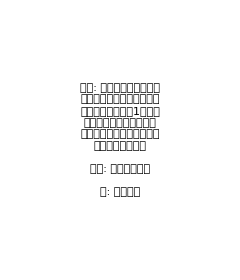
-Graphics- | -Graphics-
 | I | II | III | IV | V | VI | VII | VIII
I | 0.002 | 0.002 | 0.14 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002
II | 0.038 | 0.038 | 0.038 | 0.038 | 0.038 | 0.038 | 0.038 | 0.038
III | 0.002 | 0.174 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002
IV | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01
V | 0.002 | 0.14 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002
VI | 0.001 | 0.001 | 0.001 | 0.001 | 0.037 | 0.001 | 0.001 | 0.001
VII | 0.037 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
VIII | 0.001 | 0.013 | 0.013 | 0.013 | 0.001 | 0.001 | 0.001 | 0.001 |  | 点数 | rank
I | 0.092 | 4
II | 0.377 | 1
III | 0.205 | 2
IV | 0.068 | 5
V | 0.092 | 3
VI | 0.055 | 8
VII | 0.055 | 7
VIII | 0.055 | 6

```mathematica
slide[2]=Grid[{{gr["g",1],txt["g",1]},{tb["g",1],rt["g",1]}},Alignment->{{Center,Center},{Top,Top}}]
```

### スライド50

```mathematica
PGscore["g",50]=Nest[nextScore[#,MtoG[l,0.9]]&,Table[1/8,{8}],50]
```

{0.1129,0.33983,0.178858,0.0772476,0.1129,0.0594212,0.0594212,0.0594212}

```mathematica
(g[50]=MtoG[l,0.9]*PGscore["g",50])//TableForm
```

0.00141125 | 0.00141125 | 0.103022 | 0.00141125 | 0.00141125 | 0.00141125 | 0.00141125 | 0.00141125
0.0424788 | 0.0424788 | 0.0424788 | 0.0424788 | 0.0424788 | 0.0424788 | 0.0424788 | 0.0424788
0.00223572 | 0.163208 | 0.00223572 | 0.00223572 | 0.00223572 | 0.00223572 | 0.00223572 | 0.00223572
0.00965595 | 0.00965595 | 0.00965595 | 0.00965595 | 0.00965595 | 0.00965595 | 0.00965595 | 0.00965595
0.00141125 | 0.103022 | 0.00141125 | 0.00141125 | 0.00141125 | 0.00141125 | 0.00141125 | 0.00141125
0.000742765 | 0.000742765 | 0.000742765 | 0.000742765 | 0.0542219 | 0.000742765 | 0.000742765 | 0.000742765
0.0542219 | 0.000742765 | 0.000742765 | 0.000742765 | 0.000742765 | 0.000742765 | 0.000742765 | 0.000742765
0.000742765 | 0.0185691 | 0.0185691 | 0.0185691 | 0.000742765 | 0.000742765 | 0.000742765 | 0.000742765

```mathematica
tb["g",50]=TableForm[Round[g[50],0.001],TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,1}]
```

| I | II | III | IV | V | VI | VII | VIII
I | 0.001 | 0.001 | 0.103 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
II | 0.042 | 0.042 | 0.042 | 0.042 | 0.042 | 0.042 | 0.042 | 0.042
III | 0.002 | 0.163 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002
IV | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01
V | 0.001 | 0.103 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
VI | 0.001 | 0.001 | 0.001 | 0.001 | 0.054 | 0.001 | 0.001 | 0.001
VII | 0.054 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
VIII | 0.001 | 0.019 | 0.019 | 0.019 | 0.001 | 0.001 | 0.001 | 0.001

```mathematica
edgeforce["g",50]=MapIndexed[If[#>0,{#2,#1}]&,g[50],{2}];
```

```mathematica
style["g",50]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/10])&,Cases[edgeforce["g",50],_List,{2}]];
```

```mathematica
gr["g",50]=AdjacencyGraph[toAdjacency[g[50]],VertexCoordinates->ellipseLayout[8,{1.4,1}],VertexLabels->vlabels["l"],DirectedEdges->True,EdgeStyle->style["g",50],ImagePadding->{{5,5},{5,5}},ImageSize->{320,320}]
```

-Graphics-

```mathematica
score["g",50]=Map[Tr[#]&,Transpose[g[50]]]
```

{0.1129,0.33983,0.178858,0.0772476,0.1129,0.0594212,0.0594212,0.0594212}

```mathematica
ranking["g",50]=Ordering[Ordering[score["g",50],All,Greater]]
```

{4,1,2,5,3,8,7,6}

```mathematica
rt["g",50]=TableForm[Inner[List,Round[score["g",50],0.001],ranking["g",50],List],TableHeadings->{vnames["l"],{"点数","rank"}}]
```

| 点数 | rank
I | 0.113 | 4
II | 0.34 | 1
III | 0.179 | 2
IV | 0.077 | 5
V | 0.113 | 3
VI | 0.059 | 8
VII | 0.059 | 7
VIII | 0.059 | 6

```mathematica
txt["g",50]=Graphics[{FontSize->16,Text[Style["左上: ランダムサーファー
モデルにより密結合された
ネットワークに、50回繰り
返し法を適応したもの、
リンクの強さは収束し
これ以上繰り返しても
変化は見られない。

左下: その結合行列

下: ランク表",TextAlignment->Left]]},ImageSize->{240,280}];
```

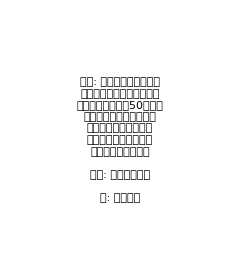
-Graphics- | -Graphics-
 | I | II | III | IV | V | VI | VII | VIII
I | 0.001 | 0.001 | 0.103 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
II | 0.042 | 0.042 | 0.042 | 0.042 | 0.042 | 0.042 | 0.042 | 0.042
III | 0.002 | 0.163 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002
IV | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01
V | 0.001 | 0.103 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
VI | 0.001 | 0.001 | 0.001 | 0.001 | 0.054 | 0.001 | 0.001 | 0.001
VII | 0.054 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
VIII | 0.001 | 0.019 | 0.019 | 0.019 | 0.001 | 0.001 | 0.001 | 0.001 |  | 点数 | rank
I | 0.113 | 4
II | 0.34 | 1
III | 0.179 | 2
IV | 0.077 | 5
V | 0.113 | 3
VI | 0.059 | 8
VII | 0.059 | 7
VIII | 0.059 | 6

```mathematica
slide[50]=Grid[{{gr["g",50],txt["g",50]},{tb["g",50],rt["g",50]}},Alignment->{{Center,Center},{Top,Top}}]
```

### アニメーション

```mathematica
animlist={slide[0],slide[1],slide[2],slide[50]};
```

```mathematica
ListAnimate[animlist]
```

## Pagerankアルゴリズムの引用/被引用行列への応用

```mathematica
numofnodes=4
```

4

```mathematica
toAdjacency[t_]:=Map[If[#>0,1,0]&,t,{2}]
```

引用被引用行列の設定

```mathematica
c={{0,0,0,3},{1,0,0,0},{2,2,0,0},{0,3,1,0}}
```

{{0,0,0,3},{1,0,0,0},{2,2,0,0},{0,3,1,0}}

```mathematica
(*(c=ReplacePart[Table[RandomChoice[{3,2,1,0,0,0,0}],{numofnodes},{numofnodes}],Table[{n,n}->0,{n,numofnodes}]])//TableForm*)
```

```mathematica
nodename=Table[IntegerString[n,"Roman"],{n,numofnodes}]
```

{I,II,III,IV}

```mathematica
vlabels[4]=Table[n->Text[Style[IntegerString[n,"Roman"],Large]],{n,numofnodes}]
```

{1→I,2→II,3→III,4→IV}

### アニメーションのコマ作成

スライド1

```mathematica
edgeforce[0]=MapIndexed[If[#>0,{#2,#1}]&,c,{2}]
```

{{Null,Null,Null,{{1,4},3}},{{{2,1},1},Null,Null,Null},{{{3,1},2},{{3,2},2},Null,Null},{Null,{{4,2},3},{{4,3},1},Null}}

```mathematica
edgeforcelabels[0]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Text[Style[ToString[#[[2]]],Medium]])&,Cases[edgeforce[0],_List,{2}]]
```

{1->4→3,2->1→1,3->1→2,3->2→2,4->2→3,4->3→1}

```mathematica
style[0]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/100])&,Cases[edgeforce[0],_List,{2}]]
```

{1->4→Thickness[3/100],2->1→Thickness[1/100],3->1→Thickness[1/50],3->2→Thickness[1/50],4->2→Thickness[3/100],4->3→Thickness[1/100]}

```mathematica
gr[0]=AdjacencyGraph[toAdjacency[c],VertexLabels->vlabels[4],EdgeLabels->edgeforcelabels[0],EdgeStyle->style[0],ImagePadding->{{0,30},{0,30}},ImageSize->{240,240}]
```

-Graphics-

```mathematica
edgeforcelabels[0]
```

{1->4→3,2->1→1,3->1→2,3->2→2,4->2→3,4->3→1}

```mathematica
tf[0]=TableForm[Map[Text[Style[ToString[#],Medium]]&,c,{2}],TableHeadings->{nodename,nodename}]
```

| I | II | III | IV
I | 0 | 0 | 0 | 3
II | 1 | 0 | 0 | 0
III | 2 | 2 | 0 | 0
IV | 0 | 3 | 1 | 0

```mathematica
tx[0]=Graphics[{FontSize->14,Text[Style["基となる引用被引用行列",TextAlignment->Left]]}];
```

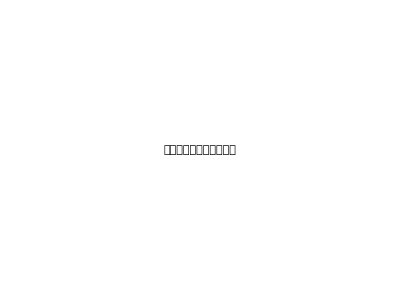
-Graphics- | -Graphics-
 | I | II | III | IV
I | 0 | 0 | 0 | 3
II | 1 | 0 | 0 | 0
III | 2 | 2 | 0 | 0
IV | 0 | 3 | 1 | 0 |

```mathematica
Grid[{{gr[0],tx[0]},{tf[0],SpanFromAbove}},ItemSize->{{1->27,2->14},{1->10,2->10}},Alignment->{{Center,Left},{Center,Left}},Spacings->{{1,0},{0,0}},Frame->True]
```

スライド2

```mathematica
m[1]=MtoG[c,0.9]
```

{{0.025,0.025,0.025,0.925},{0.925,0.025,0.025,0.025},{0.475,0.475,0.025,0.025},{0.025,0.7,0.25,0.025}}

```mathematica
edgeforce[1]=MapIndexed[If[#>0,{#2,#1}]&,m[1],{2}]
```

{{{{1,1},0.025},{{1,2},0.025},{{1,3},0.025},{{1,4},0.925}},{{{2,1},0.925},{{2,2},0.025},{{2,3},0.025},{{2,4},0.025}},{{{3,1},0.475},{{3,2},0.475},{{3,3},0.025},{{3,4},0.025}},{{{4,1},0.025},{{4,2},0.7},{{4,3},0.25},{{4,4},0.025}}}

```mathematica
edgeforcelabels[1]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Text[Style[ToString[#[[2]]],Medium]])&,Cases[edgeforce[1],_List,{2}]]
```

{1->1→0.025,1->2→0.025,1->3→0.025,1->4→0.925,2->1→0.925,2->2→0.025,2->3→0.025,2->4→0.025,3->1→0.475,3->2→0.475,3->3→0.025,3->4→0.025,4->1→0.025,4->2→0.7,4->3→0.25,4->4→0.025}

```mathematica
style[1]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/50])&,Cases[edgeforce[1],_List,{2}]]
```

{1->1→Thickness[0.0005],1->2→Thickness[0.0005],1->3→Thickness[0.0005],1->4→Thickness[0.0185],2->1→Thickness[0.0185],2->2→Thickness[0.0005],2->3→Thickness[0.0005],2->4→Thickness[0.0005],3->1→Thickness[0.0095],3->2→Thickness[0.0095],3->3→Thickness[0.0005],3->4→Thickness[0.0005],4->1→Thickness[0.0005],4->2→Thickness[0.014],4->3→Thickness[0.005],4->4→Thickness[0.0005]}

```mathematica
toAdjacency[m[1]]
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}

```mathematica
gr[1]=AdjacencyGraph[toAdjacency[MtoG[c,0.9]],DirectedEdges->True,VertexLabels->vlabels[4],EdgeStyle->style[1],(*EdgeLabels->edgeforcelabels[1],*)ImagePadding->{{5,5},{0,5}},ImageSize->{300,300}]
```

-Graphics-

```mathematica
tx[1]=Graphics[{FontSize->14,Text[Style["ランダムサーファーモデル
による結合行列",TextAlignment->Left]]}];
```

```mathematica
tf[1]=TableForm[Map[Text[Style[ToString[#],Medium]]&,m[1],{2}],TableHeadings->{nodename,nodename}]
```

| I | II | III | IV
I | 0.025 | 0.025 | 0.025 | 0.925
II | 0.925 | 0.025 | 0.025 | 0.025
III | 0.475 | 0.475 | 0.025 | 0.025
IV | 0.025 | 0.7 | 0.25 | 0.025

```mathematica
sc[1]=Table[1/numofnodes,{numofnodes}]
```

{1/4,1/4,1/4,1/4}

```mathematica
sct[1]=TableForm[Transpose[{sc[1]}]//N,TableHeadings->{nodename,{"点数"}}]
```

| 点数
I | 0.25
II | 0.25
III | 0.25
IV | 0.25

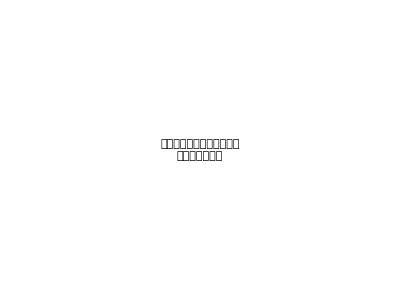
-Graphics- | -Graphics-
 | I | II | III | IV
I | 0.025 | 0.025 | 0.025 | 0.925
II | 0.925 | 0.025 | 0.025 | 0.025
III | 0.475 | 0.475 | 0.025 | 0.025
IV | 0.025 | 0.7 | 0.25 | 0.025 |  | 点数
I | 0.25
II | 0.25
III | 0.25
IV | 0.25

```mathematica
Grid[{{gr[1],tx[1]},{tf[1],sct[1]}},ItemSize->{{1->27,2->14},{1->10,2->10}},Alignment->{{Center,Left},{Center,Left}},Spacings->{{1,0},{0,0}},Frame->True]
```

スライド last

```mathematica
m[1]=MtoG[c,0.9]
```

{{0.025,0.025,0.025,0.925},{0.925,0.025,0.025,0.025},{0.475,0.475,0.025,0.025},{0.025,0.7,0.25,0.025}}

```mathematica
PGscore["m[5]"]=Nest[nextScore[#,MtoG[m[1],0.9]]&,Table[1/numofnodes,{numofnodes}],5]
```

{0.323921,0.259697,0.103197,0.313185}

```mathematica
PGscore["m[25]"]=Nest[nextScore[#,MtoG[m[1],0.9]]&,Table[1/numofnodes,{numofnodes}],25]
```

{0.314234,0.275071,0.108688,0.302006}

```mathematica
PGscore["m[50]"]=Nest[nextScore[#,MtoG[m[1],0.9]]&,Table[1/numofnodes,{numofnodes}],50]
```

{0.314268,0.275009,0.108666,0.302057}

```mathematica
PGscore["m[100]"]=Nest[nextScore[#,MtoG[m[1],0.9]]&,Table[1/numofnodes,{numofnodes}],100]
```

{0.314267,0.275009,0.108666,0.302057}

```mathematica
Tr[PGscore["m[50]"]]
```

1.

```mathematica
PGscore["m[100]"].MtoG[m[1],0.9]
```

{0.314267,0.275009,0.108666,0.302057}

```mathematica
(fixedtable["m[100]"]=MtoG[m[1],0.9]*PGscore["m[100]"])//TableForm
```

0.0149277 | 0.0149277 | 0.0149277 | 0.269484
0.235821 | 0.0130629 | 0.0130629 | 0.0130629
0.0491716 | 0.0491716 | 0.00516166 | 0.00516166
0.0143477 | 0.197847 | 0.0755142 | 0.0143477

```mathematica
Map[Tr[#]&,Transpose[fixedtable["m[100]"]]]
```

{0.314267,0.275009,0.108666,0.302057}

```mathematica
edgeforce["last"]=MapIndexed[If[#>0,{#2,#1}]&,fixedtable["m[100]"],{2}]
```

{{{{1,1},0.0149277},{{1,2},0.0149277},{{1,3},0.0149277},{{1,4},0.269484}},{{{2,1},0.235821},{{2,2},0.0130629},{{2,3},0.0130629},{{2,4},0.0130629}},{{{3,1},0.0491716},{{3,2},0.0491716},{{3,3},0.00516166},{{3,4},0.00516166}},{{{4,1},0.0143477},{{4,2},0.197847},{{4,3},0.0755142},{{4,4},0.0143477}}}

```mathematica
edgeforcelabels["last"]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Text[Style[ToString[Round[#[[2]],0.001]],Medium]])&,Cases[edgeforce["last"],_List,{2}]]
```

{1->1→0.015,1->2→0.015,1->3→0.015,1->4→0.269,2->1→0.236,2->2→0.013,2->3→0.013,2->4→0.013,3->1→0.049,3->2→0.049,3->3→0.005,3->4→0.005,4->1→0.014,4->2→0.198,4->3→0.076,4->4→0.014}

```mathematica
style["last"]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/25])&,Cases[edgeforce["last"],_List,{2}]]
```

{1->1→Thickness[0.000597108],1->2→Thickness[0.000597108],1->3→Thickness[0.000597108],1->4→Thickness[0.0107794],2->1→Thickness[0.00943282],2->2→Thickness[0.000522518],2->3→Thickness[0.000522518],2->4→Thickness[0.000522518],3->1→Thickness[0.00196686],3->2→Thickness[0.00196686],3->3→Thickness[0.000206466],3->4→Thickness[0.000206466],4->1→Thickness[0.000573908],4->2→Thickness[0.00791388],4->3→Thickness[0.00302057],4->4→Thickness[0.000573908]}

```mathematica
gr[1]=AdjacencyGraph[toAdjacency[fixedtable["m[100]"]],DirectedEdges->True,VertexLabels->vlabels[4],EdgeStyle->style["last"],(*EdgeLabels->edgeforcelabels["last"],*)ImagePadding->{{5,5},{0,5}},ImageSize->{300,300}]
```

-Graphics-

```mathematica
gr[1]=AdjacencyGraph[toAdjacency[fixedtable["m[100]"]],DirectedEdges->True,VertexLabels->vlabels[4],EdgeStyle->style["last"],EdgeLabels->edgeforcelabels["last"],ImagePadding->{{5,5},{0,5}},ImageSize->{300,300}]
```

-Graphics-

## 作業メモおよび確認

スコアの算出

```mathematica
PGscore["c"]=Nest[nextScore[#,MtoG[c,0.9]]&,Table[1/numofnodes,{numofnodes}],40]
```

{0.317192,0.277365,0.0948946,0.310549}

```mathematica
Map[#/Tr[#]&,Eigensystem[Transpose[MtoG[c,0.9]]][[2]][[1]],{0}]
```

{0.317272,0.27731,0.0948726,0.310545}

収束していることの確認

```mathematica
PGscore["c"].MtoG[c,0.9]
```

{0.317331,0.277323,0.0948734,0.310472}

```mathematica
Map[Tr[#]&,MtoG[c,0.9]*PGscore["c"]]
```

{0.317192,0.277365,0.0948946,0.310549}

重みつき引用被引用行列

```mathematica
MtoG[c,0.9]*PGscore["c"]//TableForm
```

0.00792979 | 0.00792979 | 0.00792979 | 0.293402
0.256563 | 0.00693413 | 0.00693413 | 0.00693413
0.045075 | 0.045075 | 0.00237237 | 0.00237237
0.00776371 | 0.217384 | 0.0776371 | 0.00776371

```mathematica
{{a,b},{k,d}}*{e,f}
```

{{a e,b e},{f k,d f}}

```mathematica
gr[1]=AdjacencyGraph[toAdjacency[MtoG[c,0.9]],DirectedEdges->True,VertexLabels->vlabels[4],EdgeStyle->style[1],EdgeLabels->edgeforcelabels[1],ImagePadding->{{0,30},{0,30}},ImageSize->{400,220}]
```

-Graphics-